```mathematica
ClearAll["Global`*"]
```

Load up packages

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Needs["ComputerArithmetic`"]
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

```mathematica
Get["funcs_for_stepMonitor_stringConv_plotSetOfInds_etc.m"]
(*Includes (as of 2018/03/29)
makeErrorData[x_,y_,yErr_]
kPlotStepMonitorData[kStepVals_]
gPlotStepMonitorData[gStepVals_]
tStringToSec[tString_]
minTidInd[tSearchString_,tStringArr_]
tPlotInds[inds_,mom_,momErr_,pRange_,xTitle_,yTitle_]
tPlotRange[ind1_,ind2_,mom_,momErr_,pRange_,xTitle_,yTitle_]
tablePlotMov[indStart_,indEnd1_,indEnd2_,mom_,momErr_,pRange_]
tablePlotsCombineAndAnimate[mov1_,mov2_]*)
```

## Define bounds of uniform distributions using 90% CIs for κ and and T dist fits

```mathematica
kappamin=1.8;
kappamax=3.3;
Tmin = 40;
Tmax=280;
nmin=0.05;
nmax=2.;
RBmin=8;
RBmax=200;
```

## Example

```mathematica
(*Specify the seed?*)
```

```mathematica
(*seed=30;*)
```

```mathematica
(*SeedRandom[seed];*)
```

## Now give it a shot

#### Select interval

```mathematica
interval=1;
```

```mathematica
interval=2;
```

```mathematica
Print[ToString@StringForm["Using interval `1` ...",interval]]
```

#### Init data

```mathematica
Switch[interval,
1,
tid={"12:00:29.790","12:00:30.421","12:00:31.051","12:00:31.682","12:00:32.313","12:00:32.943","12:00:33.574","12:00:34.205","12:00:34.835","12:00:35.466","12:00:36.096","12:00:36.727","12:00:37.358","12:00:46.187","12:00:46.817","12:00:47.448","12:00:48.079","12:00:48.709"};
jData={{1330.56,1.144},{1205.12,1.071},{1012.48,0.973},{1012.48,0.965},{913.92,0.93},{777.28,0.922},{840.,0.911},{777.28,0.791},{777.28,0.803},{840.,0.839},{913.92,0.821},{913.92,0.864},{1012.48,0.892},{934.08,0.774},{741.44,0.712},{592.48,0.611},{480.48,0.554},{412.72,0.531}};
jErrData={{{1330.56,1.144},ErrorBar[0.057]},{{1205.12,1.071},ErrorBar[0.046]},{{1012.48,0.973},ErrorBar[0.035]},{{1012.48,0.965},ErrorBar[0.035]},{{913.92,0.93},ErrorBar[0.041]},{{777.28,0.922},ErrorBar[0.047]},{{840.,0.911},ErrorBar[0.041]},{{777.28,0.791},ErrorBar[0.049]},{{777.28,0.803},ErrorBar[0.04]},{{840.,0.839},ErrorBar[0.039]},{{913.92,0.821},ErrorBar[0.039]},{{913.92,0.864},ErrorBar[0.043]},{{1012.48,0.892},ErrorBar[0.041]},{{934.08,0.774},ErrorBar[0.047]},{{741.44,0.712},ErrorBar[0.048]},{{592.48,0.611},ErrorBar[0.043]},{{480.48,0.554},ErrorBar[0.045]},{{412.72,0.531},ErrorBar[0.05]}};
jWt={307.7870113881194,472.5897920604915,816.3265306122448,816.3265306122448,594.8839976204639,452.6935264825713,594.8839976204639,416.4931278633902,625.,657.4621959237344,657.4621959237344,540.8328826392645,594.8839976204639,452.6935264825713,434.02777777777777,540.8328826392645,493.8271604938272,399.99999999999994};
potErr={159.53,159.53,116.82,116.82,116.82,79.76,79.76,79.76,79.76,79.76,116.82,116.82,116.82,134.77,79.76,67.39,67.39,63.92};
curErr={0.057,0.046,0.035,0.035,0.041,0.047,0.041,0.049,0.04,0.039,0.039,0.043,0.041,0.047,0.048,0.043,0.045,0.05};,
2,
tid={"12:01:22.766","12:01:23.397","12:01:24.027","12:01:24.658","12:01:25.289","12:01:25.919","12:01:26.550","12:01:27.181","12:01:27.811","12:01:28.442","12:01:29.073","12:01:29.703"};
jData={{884.8,1.618},{913.92,1.696},{913.92,1.473},{913.92,1.342},{913.92,1.384},{913.92,1.317},{616.,1.177},{616.,1.25},{566.72,1.166},{529.76,0.984},{393.12,0.783},{346.08,0.834}};
jErrData={{{884.8,1.618},ErrorBar[0.057]},{{913.92,1.696},ErrorBar[0.062]},{{913.92,1.473},ErrorBar[0.054]},{{913.92,1.342},ErrorBar[0.124]},{{913.92,1.384},ErrorBar[0.204]},{{913.92,1.317},ErrorBar[0.11]},{{616.,1.177},ErrorBar[0.105]},{{616.,1.25},ErrorBar[0.1]},{{566.72,1.166},ErrorBar[0.112]},{{529.76,0.984},ErrorBar[0.152]},{{393.12,0.783},ErrorBar[0.087]},{{346.08,0.834},ErrorBar[0.044]}};
jWt={307.7870113881194,260.1456815816858,342.93552812071334,65.03642039542144,24.02921953094964,82.64462809917356,90.702947845805,99.99999999999999,79.71938775510203,43.282548476454295,132.11784912141633,516.5289256198348};
potErr={134.77,116.82,116.82,116.82,116.82,116.82,79.76,79.76,79.76,67.39,67.39,39.88};
curErr = {0.057,0.062,0.054,0.124,0.204,0.11,0.105,0.1,0.112,0.152,0.087,0.044};
]
potVal=jData[[;;,1]];
nPots=Length@potVal;
```

```mathematica
curVal=jData[[;;,2]];
```

#### Which fit method to use?

```mathematica
(*fitMethod="LevenbergMarquardt";*)
```

```mathematica
(*fitMethod="ConjugateGradient";*)
(*fitMethod="Gradient";*)
(*fitMethod="Newton";*)
```

```mathematica
fitMethod={"NMinimize",Method->"NelderMead"};
```

```mathematica
fitMethod={"NMinimize",Method->"DifferentialEvolution"};
```

```mathematica
fitMethod={"NMinimize",Method->"SimulatedAnnealing"};
```

```mathematica
fitMethod={"NMinimize",Method->"RandomSearch"};
```

```mathematica
fitMethod=Automatic;
```

```mathematica
If[Length@fitMethod==2,fitMethodString=ToString@StringForm["`1`__`2`",fitMethod[[1]],ToString@Values@fitMethod[[2]]],fitMethodString=fitMethod];
```

#### Bounds

```mathematica
minFitT=115;
maxFitT=125;
minFitRB=2;
maxFitRB=100;
minFitN=0.1;
maxFitN=2;
minFitKappa=1.8;
maxFitKappa=35;
```

#### Init model setter uppers

Now Kappa

```mathematica
(*kModel = JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
gModel = JVMaxwellian[pot,gFitRB,gFitT,gFitN];*)
```

```mathematica
Options[kFitVarSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kFitVarSetup[OptionsPattern[]]:=Module[{fitVars},
fitVars={};
If[OptionValue[fixN]==False,fitVars=Append[fitVars,{kFitN,kFitNinit}]];
If[OptionValue[fixT]==False,fitVars=Append[fitVars,{kFitT,kFitTinit}]];
If[OptionValue[fixRB]==False,fitVars=Append[fitVars,{kFitRB,kFitRBinit}]];
If[OptionValue[fixKappa]==False,fitVars=Append[fitVars,{kFitKappa,kFitKappainit}]];
fitVars
]
```

```mathematica
Options[kConstraintSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kConstraintSetup[OptionsPattern[]]:=Module[{constraints},
constraints={};
If[OptionValue[fixN]==False,constraints=Append[constraints,minFitN<kFitN<maxFitN]];
If[OptionValue[fixT]==False,constraints=Append[constraints,minFitT<kFitT<maxFitT]];
If[OptionValue[fixRB]==False,constraints=Append[constraints,minFitRB<kFitRB<maxFitRB]];
If[OptionValue[fixKappa]==False,constraints=Append[constraints,minFitKappa<kFitKappa<maxFitKappa]];
constraints
]
```

```mathematica
Options[kFitModelSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kFitModelSetup[OptionsPattern[]]:=Module[{fitModel},
fitModel=JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
If[NumberQ@OptionValue[fixN],fitModel=fitModel/.{kFitN->OptionValue[fixN]}];
If[NumberQ@OptionValue[fixT],fitModel=fitModel/.{kFitT->OptionValue[fixT]}];
If[NumberQ@OptionValue[fixRB],fitModel=fitModel/.{kFitRB->OptionValue[fixRB]}];
If[NumberQ@OptionValue[fixKappa],fitModel=fitModel/.{kFitKappa->OptionValue[fixKappa]}];
fitModel
]
```

```mathematica
Options[kFitOutputSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kFitOutputSetup[OptionsPattern[]]:=Module[{fitOutput},
fitOutput={kFitN,kFitT,kFitRB,kFitKappa,kFitChi2red};
If[NumberQ@OptionValue[fixN],fitOutput=fitOutput/.{kFitN->OptionValue[fixN]}];
If[NumberQ@OptionValue[fixT],fitOutput=fitOutput/.{kFitT->OptionValue[fixT]}];
If[NumberQ@OptionValue[fixRB],fitOutput=fitOutput/.{kFitRB->OptionValue[fixRB]}];
If[NumberQ@OptionValue[fixKappa],fitOutput=fitOutput/.{kFitKappa->OptionValue[fixKappa]}];
fitOutput
]
```

```mathematica
Options[kFitValAddsSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kFitValAddsSetup[OptionsPattern[]]:=Module[{fitValAdds},
fitValAdds={};
If[NumberQ@OptionValue[fixN],fitValAdds=Append[fitValAdds,kFitN->OptionValue[fixN]];];
If[NumberQ@OptionValue[fixT],fitValAdds=Append[fitValAdds,kFitT->OptionValue[fixT]];];
If[NumberQ@OptionValue[fixRB],fitValAdds=Append[fitValAdds,kFitRB->OptionValue[fixRB]];];
If[NumberQ@OptionValue[fixKappa],fitValAdds=Append[fitValAdds,kFitKappa->OptionValue[fixKappa]];];
fitValAdds
]
```

```mathematica
Options[kDOFSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kDOFSetup[OptionsPattern[]]:=Module[{count},
count=4;
If[NumberQ@OptionValue[fixN],count--];
If[NumberQ@OptionValue[fixT],count--];
If[NumberQ@OptionValue[fixRB],count--];
If[NumberQ@OptionValue[fixKappa],count--];
count
]
```

Now Maxwellian setup

```mathematica
Options[gFitVarSetup]={fixT->False,fixN->False,fixRB-> False};
gFitVarSetup[OptionsPattern[]]:=Module[{fitVars},
fitVars={};
If[OptionValue[fixN]==False,fitVars=Append[fitVars,{gFitN,gFitNinit}]];
If[OptionValue[fixT]==False,fitVars=Append[fitVars,{gFitT,gFitTinit}]];
If[OptionValue[fixRB]==False,fitVars=Append[fitVars,{gFitRB,gFitRBinit}]];
fitVars
]
```

```mathematica
Options[gConstraintSetup]={fixT->False,fixN->False,fixRB-> False};
gConstraintSetup[OptionsPattern[]]:=Module[{constraints},
constraints={};
If[OptionValue[fixN]==False,constraints=Append[constraints,minFitN<gFitN<maxFitN]];
If[OptionValue[fixT]==False,constraints=Append[constraints,minFitT<gFitT<maxFitT]];
If[OptionValue[fixRB]==False,constraints=Append[constraints,minFitRB<gFitRB<maxFitRB]];
constraints
]
```

```mathematica
Options[gFitModelSetup]={fixT->False,fixN->False,fixRB-> False};
gFitModelSetup[OptionsPattern[]]:=Module[{fitModel},
fitModel=JVMaxwellian[pot,gFitRB,gFitT,gFitN];
If[NumberQ@OptionValue[fixN],fitModel=fitModel/.{gFitN->OptionValue[fixN]}];
If[NumberQ@OptionValue[fixT],fitModel=fitModel/.{gFitT->OptionValue[fixT]}];
If[NumberQ@OptionValue[fixRB],fitModel=fitModel/.{gFitRB->OptionValue[fixRB]}];
fitModel
]
```

```mathematica
Options[gFitOutputSetup]={fixT->False,fixN->False,fixRB-> False};
gFitOutputSetup[OptionsPattern[]]:=Module[{fitOutput},
fitOutput={gFitN,gFitT,gFitRB,gFitKappa,gFitChi2red};
If[NumberQ@OptionValue[fixN],fitOutput=fitOutput/.{gFitN->OptionValue[fixN]}];
If[NumberQ@OptionValue[fixT],fitOutput=fitOutput/.{gFitT->OptionValue[fixT]}];
If[NumberQ@OptionValue[fixRB],fitOutput=fitOutput/.{gFitRB->OptionValue[fixRB]}];
fitOutput
]
```

```mathematica
Options[gFitValAddsSetup]={fixT->False,fixN->False,fixRB-> False};
gFitValAddsSetup[OptionsPattern[]]:=Module[{fitValAdds},
fitValAdds={};
If[NumberQ@OptionValue[fixN],fitValAdds=Append[fitValAdds,gFitN->OptionValue[fixN]];];
If[NumberQ@OptionValue[fixT],fitValAdds=Append[fitValAdds,gFitT->OptionValue[fixT]];];
If[NumberQ@OptionValue[fixRB],fitValAdds=Append[fitValAdds,gFitRB->OptionValue[fixRB]];];
fitValAdds
]
```

```mathematica
Options[gDOFSetup]={fixT->False,fixN->False,fixRB-> False};
gDOFSetup[OptionsPattern[]]:=Module[{count},
count=3;
If[NumberQ@OptionValue[fixN],count--];
If[NumberQ@OptionValue[fixT],count--];
If[NumberQ@OptionValue[fixRB],count--];
count
]
```

```mathematica
Options[genMCStartupMessage]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
genMCStartupMessage[OptionsPattern[]]:=Module[{count},
Print[ToString@StringForm["Interval: `1`",interval]];
If[NumberQ@OptionValue[fixN],Print[ToString@StringForm["fixN    : `1`",OptionValue[fixN]]]];
If[NumberQ@OptionValue[fixT],Print[ToString@StringForm["fixT    : `1`",OptionValue[fixT]]]];
If[NumberQ@OptionValue[fixRB],Print[ToString@StringForm["fixRB   : `1`",OptionValue[fixRB]]]];
If[NumberQ@OptionValue[fixKappa],Print[ToString@StringForm["fixKappa: `1`",OptionValue[fixKappa]]]];
]
```

#### Now fixies

```mathematica
fixTVal=180;
fixNVal=False;
fixRBVal= False;
fixKappaVal= False;
```

#### Init models

```mathematica
kModel=kFitModelSetup[fixT->fixTVal,fixN->fixNVal,fixRB->fixRBVal,fixKappa->fixKappaVal];
gModel=gFitModelSetup[fixT->fixTVal,fixN->fixNVal,fixRB->fixRBVal];
```

```mathematica
kFitVars:=kFitVarSetup[fixT->fixTVal,fixN->fixNVal,fixRB->fixRBVal,fixKappa->fixKappaVal];
gFitVars:=gFitVarSetup[fixT->fixTVal,fixN->fixNVal,fixRB->fixRBVal];
```

```mathematica
kConstraints=kConstraintSetup[fixT->fixTVal,fixN->fixNVal,fixRB->fixRBVal,fixKappa->fixKappaVal];
gConstraints=gConstraintSetup[fixT->fixTVal,fixN->fixNVal,fixRB->fixRBVal];
```

```mathematica
kFitOutput:=kFitOutputSetup[fixT->fixTVal,fixN->fixNVal,fixRB->fixRBVal,fixKappa->fixKappaVal];
gFitOutput:=gFitOutputSetup[fixT->fixTVal,fixN->fixNVal,fixRB->fixRBVal];
```

```mathematica
kFitValAdds=kFitValAddsSetup[fixT->fixTVal,fixN->fixNVal,fixRB->fixRBVal,fixKappa->fixKappaVal];
gFitValAdds=gFitValAddsSetup[fixT->fixTVal,fixN->fixNVal,fixRB->fixRBVal];
```

```mathematica
kDOF=kDOFSetup[fixT->fixTVal,fixN->fixNVal,fixRB->fixRBVal,fixKappa->fixKappaVal];
gDOF=gDOFSetup[fixT->fixTVal,fixN->fixNVal,fixRB->fixRBVal];
```

Unconstrain if fitMethod requires it

```mathematica
If[Head@fitMethod==String,If[
fitMethod=="LevenbergMarquardt"||fitMethod=="ConjugateGradient",kConstraints=None;gConstraints=None;kCombConstraints=None;gCombConstraints=None;kDoubledConstraints=None;gDoubledConstraints=None;]];
```

#### Initial fit

```mathematica
kinitParams = RandomReal/@{{nmin,nmax},{Tmin,Tmax},{RBmin,RBmax},{kappamin,kappamax}};
{kFitNinit,kFitTinit,kFitRBinit,kFitKappainit}=kinitParams;
ginitParams = RandomReal/@{{nmin,nmax},{Tmin,Tmax},{RBmin,RBmax}};
{gFitNinit,gFitTinit,gFitRBinit}=ginitParams;
```

```mathematica
kInitialFit=NonlinearModelFit[jData,(If[Length@kConstraints≠0,{kModel,kConstraints},kModel]),kFitVars,pot,Weights->jWt,VarianceEstimatorFunction->(1&),Method->fitMethod];
gInitialFit=NonlinearModelFit[jData,{gModel,gConstraints},gFitVars,pot,Weights->jWt,VarianceEstimatorFunction->(1&),Method->fitMethod];
```

```mathematica
kInitialFitVals:=Append[Flatten@Append[kInitialFit["BestFitParameters"],kFitValAdds],kFitChi2red->Total[(kInitialFit["FitResiduals"])^2*jWt]/kDOF]
```

```mathematica
gInitialFitVals:=Append[Flatten@Append[gInitialFit["BestFitParameters"],gFitValAdds],gFitChi2red->Total[(gInitialFit["FitResiduals"])^2*jWt]/gDOF]
```

```mathematica
MCStartupMessage:=genMCStartupMessage[fixT->fixTVal,fixN->fixNVal,fixRB->fixRBVal,fixKappa->fixKappaVal];
```

#### Setup plot ranges

```mathematica
minPot=Min[potVal ]* 8/10;maxPot=Max[potVal]*1.1;
```

```mathematica
minJ=0;maxJ=Max[curVal]*1.1;
```

#### Other plot stuff

```mathematica
parNames=Style[#,Bold]&/@{"T_m    : ","n_m    : ","R_B   : ","χ_red^2   :"};
pTableVSpace=0.5;
pTableFontSize=14;
pTableScaledLoc={0.12,0.65};
```

```mathematica
titleSize=20;
```

```mathematica
axesLabelSize=18;
```

```mathematica
gJVVals=(MapThread[NumberForm,{({gFitT,gFitN}/.gInitialFitVals),{{3,0},{3,2}}}])~Join~{ScientificForm[gFitRB,3]/.gInitialFitVals}~Join~{NumberForm[gFitChi2red,3]/.gInitialFitVals};
kJVVals=(MapThread[NumberForm,{({kFitT,kFitN}/.kInitialFitVals),{{3,0},{3,2}}}])~Join~{ScientificForm[kFitRB,3]/.kInitialFitVals}~Join~{NumberForm[kFitChi2red,3]/.kInitialFitVals};
```

```mathematica
JVParTable=Text[Grid[Transpose[{{Style["Maxwell",Bold,(ColorData[97,"ColorList"])[[1]]]}~Join~parNames~Join~{Style["Kappa  :",Bold,(ColorData[97,"ColorList"])[[2]]]}~Join~parNames,{""}~Join~gJVVals~Join~{(ToString@StringForm["`1`",NumberForm[kFitKappa/.kInitialFitVals,3]])}~Join~kJVVals}],Alignment->".",Spacings->{0,pTableVSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
initTitle=StringJoin@Riffle[tid[[{1,-1}]],"–"];
```

#### Ze plot

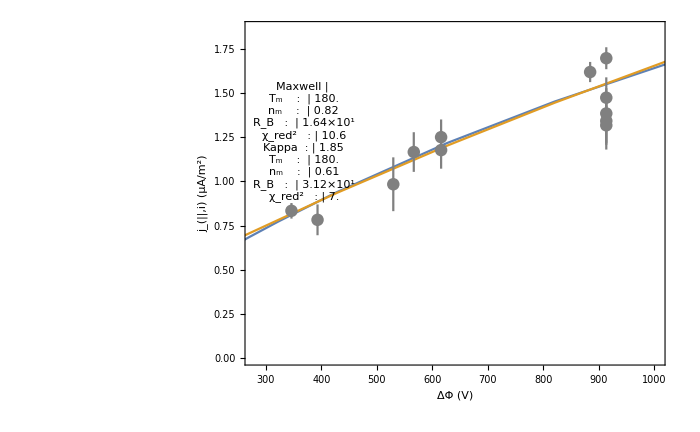

```mathematica
JVInitFitPlot=Show[Plot[{kInitialFit[pot],gInitialFit[pot]},{pot,20,10000},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["J-V Fit (`1`)",initTitle],Bold,titleSize]}},ImageSize->700,FrameStyle->Directive[Black,axesLabelSize],Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jErrData,PlotStyle->Gray]]
```

## Still need to automate variation in ΔΦ, followed by variation in J

#### Now all the fits

```mathematica
countItvl=50;
```

```mathematica
inds=Range[1,nPots];
```

```mathematica
genMCError:=RandomVariate[NormalDistribution[],nPots]*curErr[[currentInds]]
```

```mathematica
genPotVals:=potVal[[currentInds]]+RandomReal[{0,1},nPots]*potErr[[currentInds]]
```

```mathematica
currentInds=RandomChoice[inds,nPots];
```

```mathematica
curMCError=genMCError;
curPotVals=genPotVals;
```

```mathematica
curError=curErr[[currentInds]];
```

```mathematica
curjData=Partition[Riffle[curPotVals,((kInitialFit[#])&/@curPotVals)+curMCError],2];
```

```mathematica
curErrData=makeErrorData[curPotVals,curjData[[;;,2]],curError];
```

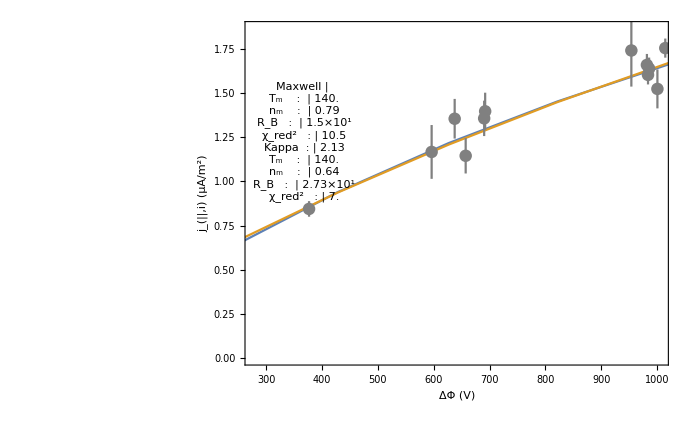

```mathematica
JVInitFitPlot=Show[Plot[{kInitialFit[pot],gInitialFit[pot]},{pot,20,10000},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["J-V Fit (`1`)",initTitle],Bold,titleSize]}},ImageSize->700,FrameStyle->Directive[Black,axesLabelSize],Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[curErrData,PlotStyle->Gray]]
```

```mathematica
currentInds=inds;
```

```mathematica
doBootstrap=False;
```

#### Kappa block

```mathematica
Block[{trials=5000, count=0,currentInds,curMCError,curPotVals,curjData,
kinitParams,kFitNinit,kFitTinit,kFitRBinit,kFitKappainit,kFit},
MCStartupMessage;
kFitVals:=Flatten@Append[{Flatten@Append[{kFit["BestFitParameters"]},kFitValAdds]},kFitChi2red->Total[(kFit["FitResiduals"])^2*curWt]/kDOF];
If[doBootstrap==False,currentInds=inds;];
Monitor[kFits=Table[
(*If[Mod[count,countItvl]==0,Print[ToString@StringForm["Count: `1`",count]]];*)
If[doBootstrap,currentInds=RandomChoice[inds,nPots];];
curMCError=genMCError;
curError=curErr[[currentInds]];
curWt=1/curError^2;
curPotVals=genPotVals;
curjData=Partition[Riffle[curPotVals,((kInitialFit[#])&/@curPotVals)+curMCError],2];
kinitParams = RandomReal/@{{nmin,nmax},{Tmin,Tmax},{RBmin,RBmax},{kappamin,kappamax}};
{kFitNinit,kFitTinit,kFitRBinit,kFitKappainit}=kinitParams;
kFit=NonlinearModelFit[curjData,(If[Length@kConstraints≠0,{kModel,kConstraints},kModel]),kFitVars,pot,Weights->curWt,VarianceEstimatorFunction->(1&),Method->fitMethod];
count++;
(*{count, kFit["BestFitParameters"],kinitParams,kFit},trials];]*)
{count,Evaluate[ kFitOutput/.kFitVals],kinitParams,kFit},trials];,count]
]
```

Interval: 1

fixT    : 140

#### Maxwell block

```mathematica
Block[{trials=5000, count=0,currentInds,curMCError,curPotVals,curjData,
ginitParams,gFitNinit,gFitTinit,gFitRBinit,gFit},
MCStartupMessage;
gFitVals:=Flatten@Append[{Flatten@Append[{gFit["BestFitParameters"]},gFitValAdds]},gFitChi2red->Total[(gFit["FitResiduals"])^2*curWt]/gDOF];
If[doBootstrap==False,currentInds=inds;];
gFits=Monitor[Table[
If[doBootstrap,currentInds=RandomChoice[inds,nPots];];
curMCError=genMCError;
curError=curErr[[currentInds]];
curWt=1/curError^2;
curPotVals=genPotVals;
curjData=Partition[Riffle[curPotVals,((gInitialFit[#])&/@curPotVals)+curMCError],2];
ginitParams = RandomReal/@{{nmin,nmax},{Tmin,Tmax},{RBmin,RBmax}};
{gFitNinit,gFitTinit,gFitRBinit}=ginitParams;
gFit=NonlinearModelFit[curjData,(If[Length@gConstraints≠0,{gModel,gConstraints},gModel]),gFitVars,pot,Weights->curWt,VarianceEstimatorFunction->(1&),Method->fitMethod];
count++;
(*{count, kFit["BestFitParameters"],kinitParams,kFit},trials];]*)
{count,Evaluate[ gFitOutput/.gFitVals],ginitParams,gFit},trials],count];]
```

Interval: 2

fixT    : 140

#### Now check ‘em out

```mathematica
kMCVals=((kFits[[;;,2]])[[;;,#]])&/@{1,2,3,4};
kMCTitles={"N (cm^-3)","T (eV)","R_B","κ"};
```

```mathematica
binSizes=Table[Automatic,4];
```

```mathematica
binSizes={{0.005},{0.2},{1},{0.2}};
```

```mathematica
MCTitle=StringJoin@Riffle[tid[[{1,-1}]],"–"];
```

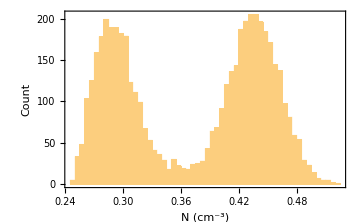
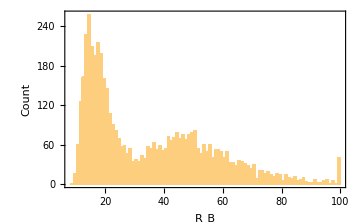
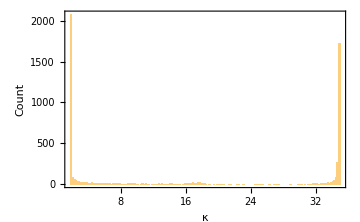
-Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[Table[Histogram[kMCVals[[MCParmInd]],binSizes[[MCParmInd]],ImageSize->Medium,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],"Count"},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

```mathematica
Row[Table[Histogram[kMCVals[[MCParmInd]],binSizes[[MCParmInd]],ImageSize->Medium,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],"Count"},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

-Graphics--Graphics--Graphics--Graphics-

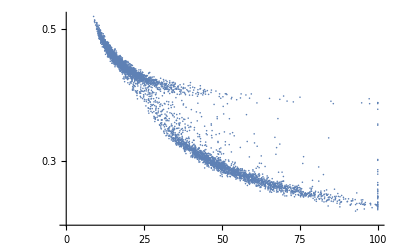

```mathematica
ListLogPlot[Partition[Riffle[kMCVals[[3]],kMCVals[[1]]],2]]
```

```mathematica
densPlotRange:=Switch[interval,1,{{0,100},{0.2,0.6}},2,{{0,80},{0.4,1.2}}];
```

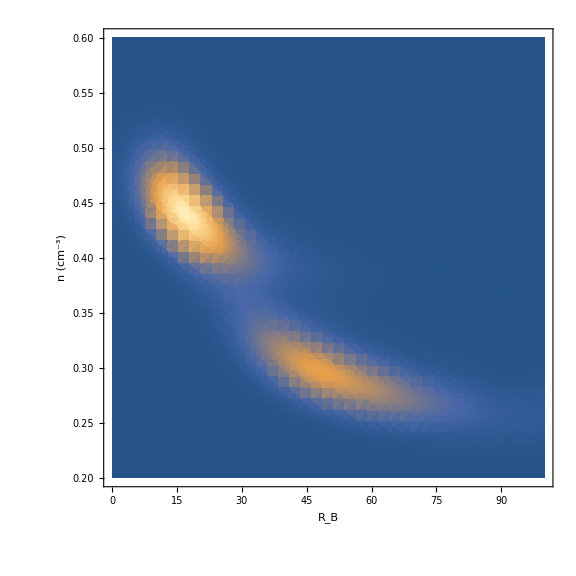

```mathematica
SmoothDensityHistogram[Partition[Riffle[kMCVals[[3]],kMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Kappa, N = `2`)",MCTitle,5000],Bold,20]}}]
```

```mathematica
SmoothDensityHistogram[Partition[Riffle[kMCVals[[3]],kMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Kappa, N = `2`)",MCTitle,5000],Bold,20]}}]
```

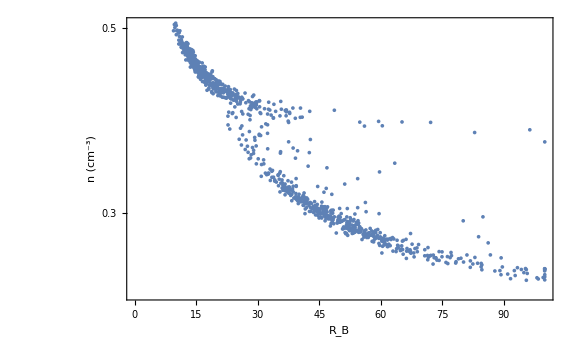

```mathematica
(*ListLogPlot[Partition[Riffle[kMCVals[[3]],kMCVals[[1]]],2],ImageSize->Large,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Kappa, N = `2`)",MCTitle,1000],Bold,20]}}]*)
```

```mathematica
gMCVals=((gFits[[;;,2]])[[;;,#]])&/@{1,2,3};
gMCTitles={"N (cm^-3)","T (eV)","R_B"};
```

Itvl 1, fixT=120 eV, nRoll= 5000

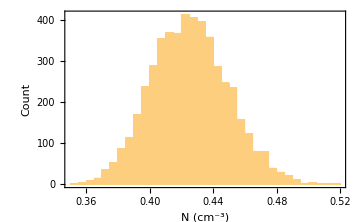
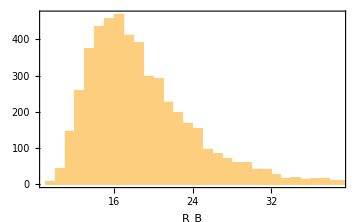
-Graphics--Graphics--Graphics-

```mathematica
Row[Table[Histogram[gMCVals[[MCParmInd]],binSizes[[MCParmInd]],ImageSize->Medium,Frame->True,FrameLabel->{gMCTitles[[MCParmInd]],If[MCParmInd==1,"Count",""]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3}}]]
```

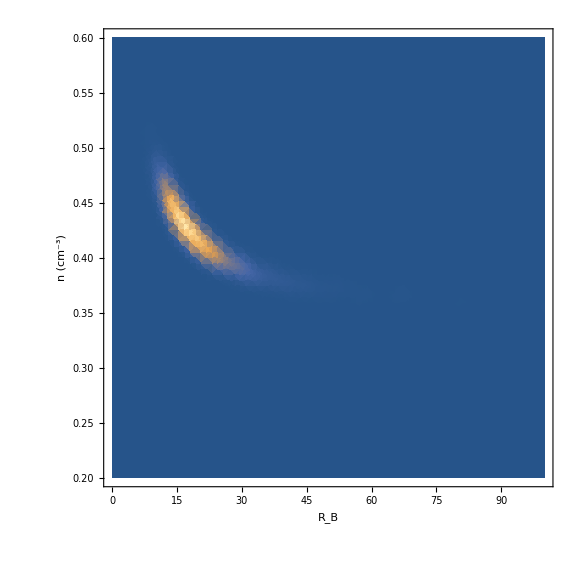

```mathematica
SmoothDensityHistogram[Partition[Riffle[gMCVals[[3]],gMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Maxwellian, N = `2`)",MCTitle,5000],Bold,20]}}]
```

Itvl 2, fixT=140 eV, nRoll= 5000

```mathematica
gMCVals=((gFits[[;;,2]])[[;;,#]])&/@{1,2,3};
gMCTitles={"N (cm^-3)","T (eV)","R_B"};
```

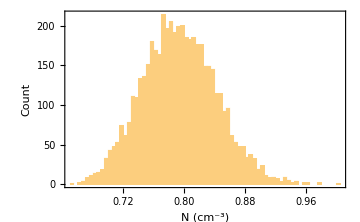
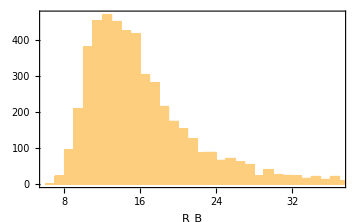
-Graphics--Graphics--Graphics-

```mathematica
Row[Table[Histogram[gMCVals[[MCParmInd]],binSizes[[MCParmInd]],ImageSize->Medium,Frame->True,FrameLabel->{gMCTitles[[MCParmInd]],If[MCParmInd==1,"Count",""]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3}}]]
```

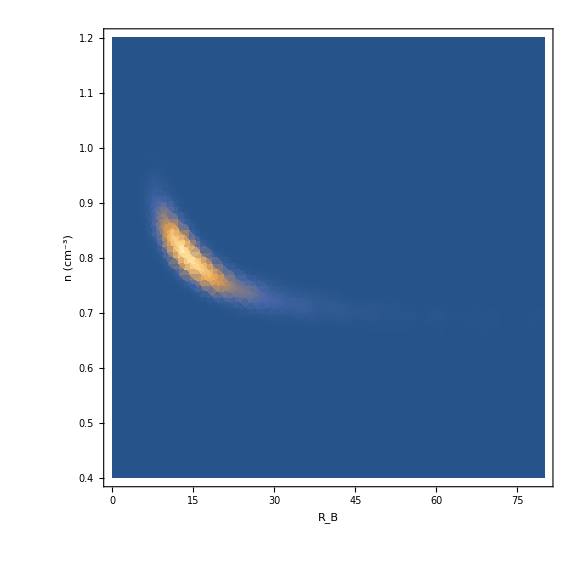

```mathematica
SmoothDensityHistogram[Partition[Riffle[gMCVals[[3]],gMCVals[[1]]],2],ImageSize->Large,PlotRange->{{0,80},{0.4,1.2}},Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Maxwellian, N = `2`)",MCTitle,5000],Bold,20]}}]
```

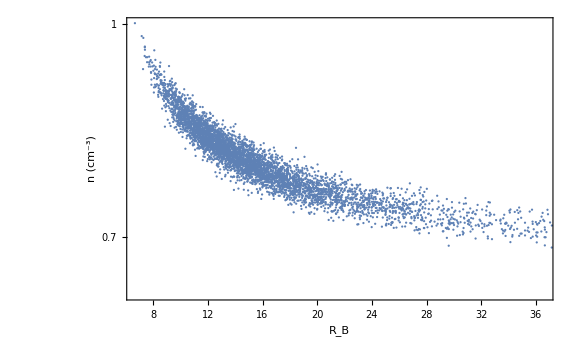

```mathematica
ListLogPlot[Partition[Riffle[gMCVals[[3]],gMCVals[[1]]],2],ImageSize->Large,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Maxwellian, N = `2`)",MCTitle,1000],Bold,20]}}]
```

Nonlinear J-V fits

```mathematica
{kFitNinit,kFitTinit,kFitRBinit,kFitKappainit} = RandomReal/@{{nmin,nmax},{Tmin,Tmax},{RBmin,RBmax},{kappamin,kappamax}}
```

{1.55357,260.639,161.051,3.28414}

```mathematica
kFit=NonlinearModelFit[jData,(If[Length@kConstraints≠0,{kModel,kConstraints},kModel]),{{kFitN,kFitNinit},{kFitT,kFitTinit},{kFitRB,kFitRBinit},{kFitKappa,kFitKappainit}},pot,Weights->jWt,VarianceEstimatorFunction->(1&),Method->fitMethod]]];
```

```mathematica
{gFit,{gFitStepVals}}=Reap[NonlinearModelFit[jData,{gModel,gConstraints},{{gFitN,gFitNinit},{gFitT,gFitTinit},{gFitRB,gFitRBinit}},pot,Weights->jWt,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{gFitRB,gFitT,gFitN,gCount++}]]];
kDOF=Length[potVal[[inds1]]]-4;
gDOF=Length[potVal[[inds1]]]-3;
{kBestN,kBestT,kBestRB,kBestKappa,kBestChi2red}=Values@kFit["BestFitParameters"]~Join~{Total[(kFit["FitResiduals"])^2*jWt]/kDOF};
{gBestN,gBestT,gBestRB,gBestChi2red}=Values@gFit["BestFitParameters"]~Join~{Total[(gFit["FitResiduals"])^2*jWt]/gDOF};
```